```mathematica
ℏ=1.0*10^-34;
kb=1.38*10^-23;
T0=6.4*10^-6;
ωt=2π *10.^5;
m171=170.936*(1.660539*10^-27);
```

```mathematica
k=(2π)/(556.*10^-9);
Γ0=2π*184.*10^3;
ωR=(ℏ k^2)/(2 m171);
η0=√(ωR/ωt)
ηOP=√(ωR/ωt)
Δls0=8 ωt/38.;
Pn[n_,T_]:=E^(-ℏ ωt n/(kb T))(1-E^(-ℏ ωt/(kb T)))
Tn[p0_]:=(ℏ ωt)/(-kb Log[1-p0])
```

0.189216

0.189216

```mathematica
Pn[0,10^-5]
```

0.365744

## master eqn.

### 171Yb F’=3/2

```mathematica
PFmF=(2*F+1)(ThreeJSymbol[{3/2,1/2},{1,q},{F,-mF}])^2;
rp=PFmF/.{F->1/2,mF->1/2,q->0};
rm=PFmF/.{F->1/2,mF->-1/2,q->-1};
Pp=rp/(rp+rm);
Pm=rm/(rp+rm);
```

```mathematica
N[{Pp,Pm}]
```

{0.666667,0.333333}

```mathematica
Ep=(2*Pp)/(1-(Pm))^2;
N[Ep]
```

3.

```mathematica
n0=6;
Hs0=({{-1/2 δ, Ω/2}, {Ω/2, 1/2 δ}});
Hs=KroneckerProduct[IdentityMatrix[n0+1],Hs0];
Hm=ω*KroneckerProduct[DiagonalMatrix[Table[(n0-n+1/2),{n,0,n0}]],IdentityMatrix[2]];
Hcs=I η Ω/2({{0, 1}, {-1, 0}});
Hcm=({{0, √6, 0, 0, 0, 0, 0}, {√6, 0, √5, 0, 0, 0, 0}, {0, √5, 0, √4, 0, 0, 0}, {0, 0, √4, 0, √3, 0, 0}, {0, 0, 0, √3, 0, √2, 0}, {0, 0, 0, 0, √2, 0, 1}, {0, 0, 0, 0, 0, 1, 0}});
Hc=KroneckerProduct[Hcm,Hcs];
MatrixForm[Hc];
H=Hs+Hm+Hc;
MatrixForm[H[[-4;;,-4;;]]]
```

(-δ/2+(3 ω)/2 | Ω/2 | 0 | (ⅈ η Ω)/2
Ω/2 | δ/2+(3 ω)/2 | -1/2 ⅈ η Ω | 0
0 | (ⅈ η Ω)/2 | -δ/2+ω/2 | Ω/2
-1/2 ⅈ η Ω | 0 | Ω/2 | δ/2+ω/2)

```mathematica
MatrixForm[H[[-8;;,-8;;]]]
```

(-δ/2+(7 ω)/2 | Ω/2 | 0 | -1/2 ⅈ √3 η Ω | 0 | 0 | 0 | 0
Ω/2 | δ/2+(7 ω)/2 | -1/2 ⅈ √3 η Ω | 0 | 0 | 0 | 0 | 0
0 | 1/2 ⅈ √3 η Ω | -δ/2+(5 ω)/2 | Ω/2 | 0 | -(ⅈ η Ω)/(√2) | 0 | 0
1/2 ⅈ √3 η Ω | 0 | Ω/2 | δ/2+(5 ω)/2 | -(ⅈ η Ω)/(√2) | 0 | 0 | 0
0 | 0 | 0 | (ⅈ η Ω)/(√2) | -δ/2+(3 ω)/2 | Ω/2 | 0 | -1/2 ⅈ η Ω
0 | 0 | (ⅈ η Ω)/(√2) | 0 | Ω/2 | δ/2+(3 ω)/2 | -1/2 ⅈ η Ω | 0
0 | 0 | 0 | 0 | 0 | (ⅈ η Ω)/2 | -δ/2+ω/2 | Ω/2
0 | 0 | 0 | 0 | (ⅈ η Ω)/2 | 0 | Ω/2 | δ/2+ω/2)

```mathematica
σm=({{0, 0}, {1, 0}});
np=3;
Om=IdentityMatrix[n0+1]+np*I*η({{0, √6, 0, 0, 0, 0, 0}, {√6, 0, √5, 0, 0, 0, 0}, {0, √5, 0, √4, 0, 0, 0}, {0, 0, √4, 0, √3, 0, 0}, {0, 0, 0, √3, 0, √2, 0}, {0, 0, 0, 0, √2, 0, 1}, {0, 0, 0, 0, 0, 1, 0}});
OLin=Γ^(1/2)KroneckerProduct[Om,σm];
MatrixForm[OLin]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
√Γ | 0 | 3 ⅈ √6 √Γ η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3 ⅈ √6 √Γ η | 0 | √Γ | 0 | 3 ⅈ √5 √Γ η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 ⅈ √5 √Γ η | 0 | √Γ | 0 | 6 ⅈ √Γ η | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 6 ⅈ √Γ η | 0 | √Γ | 0 | 3 ⅈ √3 √Γ η | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 3 ⅈ √3 √Γ η | 0 | √Γ | 0 | 3 ⅈ √2 √Γ η | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 ⅈ √2 √Γ η | 0 | √Γ | 0 | 3 ⅈ √Γ η | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 ⅈ √Γ η | 0 | √Γ | 0)

```mathematica
Ωc=2π*1.5*10^4;
Γs=2π*3*10^3;
Hn=H/.{δ->-ωt,ω->ωt,Ω->Ωc,η->η0};
OLinn=OLin/.{Γ->Γs,η->ηOP};
Ttot=(5π)/(η0 Min[{Γs,Ωc}])
Pns=Table[Pn[n,T0],{n,0,n0}];
Pns[[n0+1]]=1-Sum[Pns[[n+1]],{n,0,n0-1}];
ρs=NDSolve[{I ρ'[t]==Hn.ρ[t]-ρ[t].Hn+I (OLinn.ρ[t].(OLinn†)-1/2 OLinn†.OLinn.ρ[t]-1/2 ρ[t].OLinn†.OLinn),ρ[0]==DiagonalMatrix[Flatten[Table[{0,Pns[[n0+1-n]]},{n,0,n0}]]]},ρ,{t,0,Ttot},AccuracyGoal->4];
```

0.00440413

```mathematica
Abs[Evaluate[ρ[ts[[i]]]/.ρs][[1,14,14]]]
```

Part::pkspec1: The expression i cannot be used as a part specification.

Part::partw: Part 14 of InterpolatingFunction[{{0., 0.00440413}}, <>][ts[[i]]] does not exist.

Abs[{InterpolatingFunction[{{0., 0.00440413}}, <>][ts⟦i⟧]}⟦1,14,14⟧]

```mathematica
ts=Subdivide[0,Ttot,200];
```

```mathematica
For[i=1,i≤Length[ts],i++,
If[Abs[Evaluate[ρ[ts[[i]]]/.ρs][[1,14,14]]] >0.98 Abs[Evaluate[ρ[Ttot]/.ρs][[1,14,14]]], Break[]]
]
ts[[i]]
```

0.000880826

```mathematica
GreaterThan[Abs[Evaluate[ρ[Ttot/2]/.ρs][[1,14,14]]]][Abs[Evaluate[ρ[Ttot]/.ρs][[1,14,14]]]]
```

True

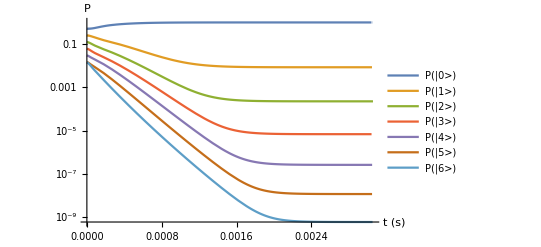

```mathematica
LogPlot[{Evaluate[ρ[t]/.ρs][[1,14,14]],Evaluate[ρ[t]/.ρs][[1,12,12]],Evaluate[ρ[t]/.ρs][[1,10,10]],Evaluate[ρ[t]/.ρs][[1,8,8]],Evaluate[ρ[t]/.ρs][[1,6,6]],Evaluate[ρ[t]/.ρs][[1,4,4]],Evaluate[ρ[t]/.ρs][[1,2,2]]},{t,0,Ttot},PlotRange->All,PlotLegends->{"P(|0>)","P(|1>)","P(|2>)","P(|3>)","P(|4>)","P(|5>)","P(|6>)"},AxesLabel->{"t (s)","P"}]
```

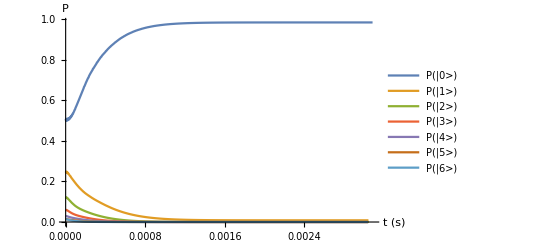

```mathematica
Plot[{Evaluate[ρ[t]/.ρs][[1,14,14]],Evaluate[ρ[t]/.ρs][[1,12,12]],Evaluate[ρ[t]/.ρs][[1,10,10]],Evaluate[ρ[t]/.ρs][[1,8,8]],Evaluate[ρ[t]/.ρs][[1,6,6]],Evaluate[ρ[t]/.ρs][[1,4,4]],Evaluate[ρ[t]/.ρs][[1,2,2]]},{t,0,Ttot},PlotRange->All,PlotLegends->{"P(|0>)","P(|1>)","P(|2>)","P(|3>)","P(|4>)","P(|5>)","P(|6>)"},AxesLabel->{"t (s)","P"}]
```

```mathematica
Tn[Abs[Evaluate[ρ[Ttot]/.ρs][[1,14,14]]]]
```

1.10942×10^-6

```mathematica
Evaluate[ρ[Ttot]/.ρs][[1,14,14]]
```

0.983493-1.25087×10^-11 ⅈ

```mathematica
ρcool=Table[Abs[Evaluate[ρ[Ttot]/.ρs][[1,i,i]]],{i,14,2,-2}]
```

{0.983493,0.00839881,0.000224768,6.85534×10^-6,2.62964×10^-7,1.1837×10^-8,6.06449×10^-10}

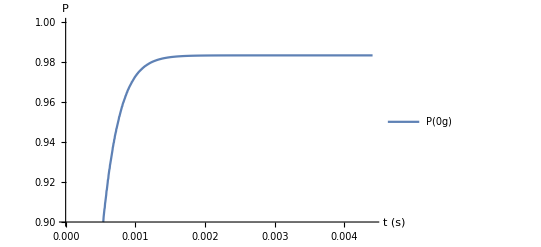

```mathematica
Plot[{Abs[Evaluate[ρ[t]/.ρs][[1,14,14]]]},{t,0,Ttot},PlotRange->{0.9,1},PlotLegends->{"P(0g)"},AxesLabel->{"t (s)","P"}]
```

check to make sure we’re not losing population

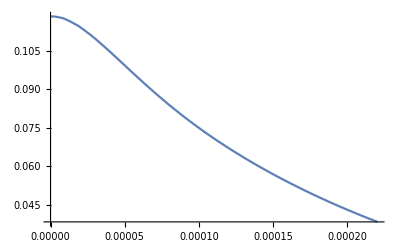

```mathematica
Plot[Sum[Evaluate[ρ[t]/.ρs][[1,i,i]],{i,1,8}],{t,0,Ttot/20},PlotRange->All]
```

#### temp Tf at the end of simulation

```mathematica
nbar=Abs[Sum[(2*(n0+1)-n)/2*Evaluate[ρ[Ttot]/.ρs][[1,n,n]],{n,2,2*(n0+1),2}]]
Tf=(ℏ ωt)/(Log[1/nbar+1]kb)
```

0.00887002

9.61791×10^-7

carrier width is:

```mathematica
Δc=1/(2π)√(Ω^2+Γ^2);
Δc/.{Ω->2π *5*10^3,Γ->Γ0/40}
```

6794.12

## loop over a few raman rabi and pumping rates

```mathematica
numGrid=7;
Pgs=Table[0,{i,1,numGrid},{j,1,numGrid}];
coolingTimes=Table[0,{i,1,numGrid},{j,1,numGrid}];
Ωcs=2π Subdivide[5.*10^3,3*10^4,numGrid-1];
Γs=2π Subdivide[0.5*10^3,1*10^4,numGrid-1];
For[ii=1,ii≤numGrid,ii++,
For[jj=1, jj≤numGrid, jj++,
Ωc=Ωcs[[ii]];
Ttot=(15π)/(η0 Min[{Γs[[jj]],Ωc}]);
ts=Subdivide[0,Ttot,200];
Hn=H/.{δ->-ωt,ω->ωt,Ω->Ωc,η->η0};
OLinn=OLin/.{Γ->Γs[[jj]],η->ηOP};
Pns=Table[Pn[n,T0],{n,0,n0}];
Pns[[n0+1]]=1-Sum[Pns[[n+1]],{n,0,n0-1}];
ρs=NDSolve[{I ρ'[t]==Hn.ρ[t]-ρ[t].Hn+I (OLinn.ρ[t].(OLinn†)-1/2 OLinn†.OLinn.ρ[t]-1/2 ρ[t].OLinn†.OLinn),ρ[0]==DiagonalMatrix[Flatten[Table[{0,Pns[[n0+1-n]]},{n,0,n0}]]]},ρ,{t,0,Ttot},AccuracyGoal->4, MaxSteps->1000000];
Pgs[[ii,jj]]=Evaluate[ρ[Ttot]/.ρs][[1,2*(n0+1),2*(n0+1)]];
For[i=1,i≤Length[ts],i++,
If[Abs[Evaluate[ρ[ts[[i]]]/.ρs][[1,14,14]]] >0.98 Abs[Evaluate[ρ[Ttot]/.ρs][[1,14,14]]], Break[]]
];
coolingTimes[[ii,jj]]=ts[[i]];
Print[{ii,jj}]
]
]
```

{1,1}

{1,2}

{1,3}

{1,4}

{1,5}

{1,6}

{1,7}

{2,1}

{2,2}

{2,3}

{2,4}

{2,5}

{2,6}

{2,7}

{3,1}

{3,2}

{3,3}

{3,4}

{3,5}

{3,6}

{3,7}

{4,1}

{4,2}

{4,3}

{4,4}

{4,5}

{4,6}

{4,7}

{5,1}

{5,2}

{5,3}

{5,4}

{5,5}

{5,6}

{5,7}

{6,1}

{6,2}

{6,3}

{6,4}

{6,5}

{6,6}

{6,7}

{7,1}

{7,2}

{7,3}

{7,4}

{7,5}

{7,6}

{7,7}

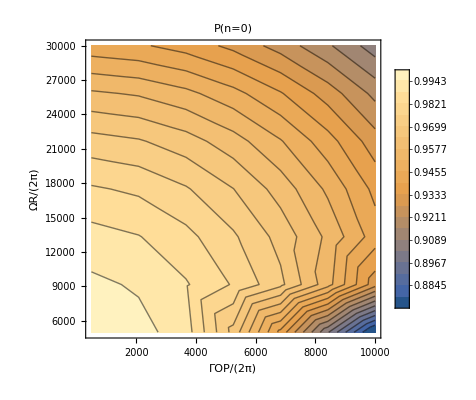

```mathematica
Pgsplot=ArrayFlatten[Table[{Γs[[j]]/(2π),Ωcs[[i]]/(2π),Abs[Pgs[[i,j]]]},{i,1,Length[Pgs]},{j,1,Length[Pgs[[1]]]}],1];
ListContourPlot[Pgsplot,PlotLegends->Automatic,FrameLabel->{"ΓOP/(2π)", "ΩR/(2π)"},Contours->20,PlotRange->{All,All,All},PlotLabel->"P(n=0)"]
```

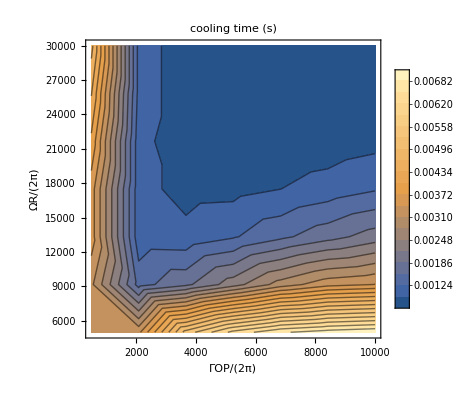

```mathematica
coolingTimesplot=ArrayFlatten[Table[{Γs[[j]]/(2π),Ωcs[[i]]/(2π),Abs[coolingTimes[[i,j]]]},{i,1,Length[coolingTimes]},{j,1,Length[coolingTimes[[1]]]}],1];
ListContourPlot[coolingTimesplot,PlotLegends->Automatic,FrameLabel->{"ΓOP/(2π)", "ΩR/(2π)"},Contours->20,PlotRange->{All,All,All},PlotLabel->"cooling time (s)"]
```

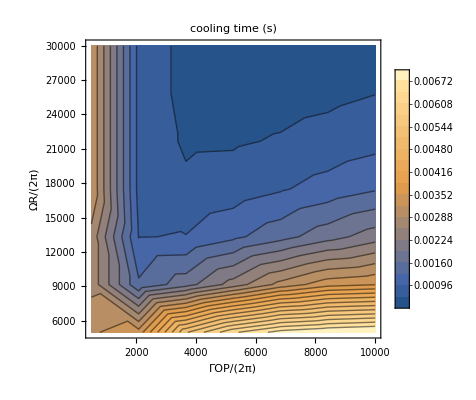

## power estimate for Raman beams

we want the scattering rate to be << raman rabi and pumping rate

```mathematica
(*Δ=2π*100.*10^6;*)
Ωr=2π*1.*10^5;
Γsc=2π*7.5*10^4;
Rsc=Γ0/(2*2π Δf);
Isat=1.39;
I0=(4*Ωr*2*π Δf)/Γ0^2;
rb=0.0015;
IOP=2*Isat((3*Γsc)/Γ0)^2;
POP=IOP*π*rb^2
P0=I0*π*rb^2
```

0.0000293837

8.35135×10^-11 Δf

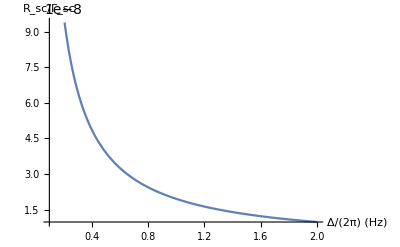

```mathematica
Plot[Rsc/Γsc,{Δf,1.*10^6,20.*10^6},AxesLabel->{"Δ/(2π) (Hz)","R_sc/Γ_sc"}]
```

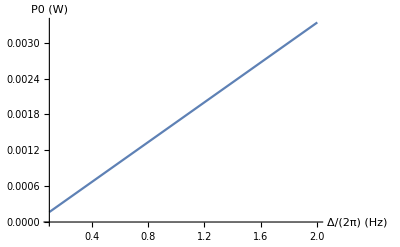

```mathematica
Plot[2*P0,{Δf,1.*10^6,20.*10^6},AxesLabel->{"Δ/(2π) (Hz)","P0 (W)"}]
```

```mathematica
10^(-0.3/10.)
```

0.933254

```mathematica
π 0.004^2/2*3*1.39
```

0.000104804

```mathematica
θ=ArcSin[0.6]
```

0.643501

```mathematica
θ*180/π
```

36.8699

```mathematica
2π*(1-Cos[θ])/(4π)
```

0.1

```mathematica
Γsc=Γ0(√(4/2))/3/(2π)
```

86738.4

```mathematica
65./115
```

0.565217

```mathematica
10.^7/(184.*10^3)
```

54.3478

```mathematica
l=0.005;
c=3.*10^8;
R1=0.99;
R2=0.3;
Δvfsr=c/(2l)
τc=1/Δvfsr 1/(-Log[R1 R2])
Δv=1/(2π τc);
Δvfsr/Δv
```

3.×10^10

2.74569×10^-11

5.17551

```mathematica
df=c/((1156.*10^-9)^2)10.^-9
```

2.24494×10^11

```mathematica
Integrate[(1-Cosh[x/dv]/Cosh[w/(2 dv)]),{x,-w/2,w/2}]
```

w-2 dv Tanh[w/(2 dv)]

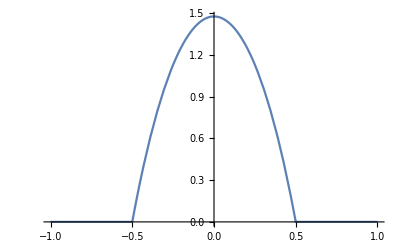

```mathematica
Plot[1/(w-2 dv Tanh[w/(2 dv)])(1-Cosh[x/dv]/Cosh[w/(2 dv)])*UnitBox[x/w]/.{w->1,dv->0.5},{x,-1,1}]
```

## light shift 3P1 and optical pumping

### 171Yb F’=3/2

```mathematica
PFmF=(2*F+1)(ThreeJSymbol[{3/2,1/2},{1,q},{F,-mF}])^2;
rp=PFmF/.{F->1/2,mF->1/2,q->0};
rm=PFmF/.{F->1/2,mF->-1/2,q->-1};
Pp=rp/(rp+rm);
Pm=rm/(rp+rm);
```

```mathematica
N[{Pp,Pm}]
```

{0.666667,0.333333}

```mathematica
Ep=(2*Pp)/(1-(Pm))^2;
N[Ep]
```

3.

```mathematica
n0=3;
Hs0=({{-δop, Ωop/2, 0}, {Ωop/2, -1/2 δ, Ω/2}, {0, Ω/2, 1/2 δ}});
Hs=KroneckerProduct[IdentityMatrix[n0+1],Hs0];
Hm=ω*KroneckerProduct[DiagonalMatrix[Table[(n0-n+1/2),{n,0,n0}]],IdentityMatrix[3]];
Hls=KroneckerProduct[DiagonalMatrix[Table[-Δls(n0-n+1/2),{n,0,n0}]],({{1, 0, 0}, {0, 0, 0}, {0, 0, 0}})];
```

```mathematica
Hcs=I({{0, Ωop/2 ηop, 0}, {-Ωop/2 ηop, 0, Ω/2 η}, {0, -Ω/2 η, 0}});
Hcm=({{0, √3, 0, 0}, {√3, 0, √2, 0}, {0, √2, 0, 1}, {0, 0, 1, 0}});
Hc=KroneckerProduct[Hcm,Hcs];
MatrixForm[Hc];
H=Hs+Hm+Hc+Hls;
```

```mathematica
MatrixForm[H]
```

(-(7 Δls)/2-δop+(7 ω)/2 | Ωop/2 | 0 | 0 | 1/2 ⅈ √3 ηop Ωop | 0 | 0 | 0 | 0 | 0 | 0 | 0
Ωop/2 | -δ/2+(7 ω)/2 | Ω/2 | -1/2 ⅈ √3 ηop Ωop | 0 | 1/2 ⅈ √3 η Ω | 0 | 0 | 0 | 0 | 0 | 0
0 | Ω/2 | δ/2+(7 ω)/2 | 0 | -1/2 ⅈ √3 η Ω | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 ⅈ √3 ηop Ωop | 0 | -(5 Δls)/2-δop+(5 ω)/2 | Ωop/2 | 0 | 0 | (ⅈ ηop Ωop)/(√2) | 0 | 0 | 0 | 0
-1/2 ⅈ √3 ηop Ωop | 0 | 1/2 ⅈ √3 η Ω | Ωop/2 | -δ/2+(5 ω)/2 | Ω/2 | -(ⅈ ηop Ωop)/(√2) | 0 | (ⅈ η Ω)/(√2) | 0 | 0 | 0
0 | -1/2 ⅈ √3 η Ω | 0 | 0 | Ω/2 | δ/2+(5 ω)/2 | 0 | -(ⅈ η Ω)/(√2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (ⅈ ηop Ωop)/(√2) | 0 | -(3 Δls)/2-δop+(3 ω)/2 | Ωop/2 | 0 | 0 | (ⅈ ηop Ωop)/2 | 0
0 | 0 | 0 | -(ⅈ ηop Ωop)/(√2) | 0 | (ⅈ η Ω)/(√2) | Ωop/2 | -δ/2+(3 ω)/2 | Ω/2 | -1/2 ⅈ ηop Ωop | 0 | (ⅈ η Ω)/2
0 | 0 | 0 | 0 | -(ⅈ η Ω)/(√2) | 0 | 0 | Ω/2 | δ/2+(3 ω)/2 | 0 | -1/2 ⅈ η Ω | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ ηop Ωop)/2 | 0 | -Δls/2-δop+ω/2 | Ωop/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ ηop Ωop | 0 | (ⅈ η Ω)/2 | Ωop/2 | -δ/2+ω/2 | Ω/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 ⅈ η Ω | 0 | 0 | Ω/2 | δ/2+ω/2)

```mathematica
σm=({{0, 0, 0}, {√Pm, 0, 0}, {√Pp, 0, 0}});
np=1;
Om=IdentityMatrix[n0+1]+np*I*ηop({{0, √3, 0, 0}, {√3, 0, √2, 0}, {0, √2, 0, 1}, {0, 0, 1, 0}});
OLin=Γ^(1/2)KroneckerProduct[Om,σm];
MatrixForm[OLin]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(√Γ)/(√3) | 0 | 0 | ⅈ √Γ ηop | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
√(2/3) √Γ | 0 | 0 | ⅈ √2 √Γ ηop | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ √Γ ηop | 0 | 0 | (√Γ)/(√3) | 0 | 0 | ⅈ √(2/3) √Γ ηop | 0 | 0 | 0 | 0 | 0
ⅈ √2 √Γ ηop | 0 | 0 | √(2/3) √Γ | 0 | 0 | (2 ⅈ √Γ ηop)/(√3) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ √(2/3) √Γ ηop | 0 | 0 | (√Γ)/(√3) | 0 | 0 | (ⅈ √Γ ηop)/(√3) | 0 | 0
0 | 0 | 0 | (2 ⅈ √Γ ηop)/(√3) | 0 | 0 | √(2/3) √Γ | 0 | 0 | ⅈ √(2/3) √Γ ηop | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (ⅈ √Γ ηop)/(√3) | 0 | 0 | (√Γ)/(√3) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ⅈ √(2/3) √Γ ηop | 0 | 0 | √(2/3) √Γ | 0 | 0)

```mathematica
Ωc=2π*6*10^3;
ΩOP=2π*2*10^4;
Γ3p1=2π*180.*10^3;
Hn=H/.{δ->-ωt,δop->0,ω->ωt,Δls->Δls0,Ω->Ωc,Ωop->ΩOP,ηop->ηOP,η->η0};
OLinn=OLin/.{Γ->Γ3p1,ηop->ηOP};
Ttot=(30π)/(η0 Min[{ΩOP/6,Ωc}])
Pns=Table[Pn[n,T0],{n,0,n0}];
Pns[[n0+1]]=1-Sum[Pns[[n+1]],{n,0,n0-1}];
ρs=NDSolve[{I ρ'[t]==Hn.ρ[t]-ρ[t].Hn+I (OLinn.ρ[t].(OLinn†)-1/2 OLinn†.OLinn.ρ[t]-1/2 ρ[t].OLinn†.OLinn),ρ[0]==DiagonalMatrix[Flatten[Table[{0,0,Pns[[n0+1-n]]},{n,0,n0}]]]},ρ,{t,0,Ttot},AccuracyGoal->4];
```

0.0237823

```mathematica
nbar=Abs[Sum[(2*(n0+1)-n)/2*Evaluate[ρ[Ttot]/.ρs][[1,n,n]],{n,2,2*(n0+1),2}]]
Tf=(ℏ ωt)/(Log[1/nbar+1]kb)
```

0.000462543

5.92902×10^-7

```mathematica
Abs[Evaluate[ρ[Ttot]/.ρs][[1,12,12]]]
```

0.995363

```mathematica
ts=Subdivide[0,Ttot,200];
```

```mathematica
For[i=1,i≤Length[ts],i++,
If[Abs[Evaluate[ρ[ts[[i]]]/.ρs][[1,12,12]]] >0.98 Abs[Evaluate[ρ[Ttot]/.ρs][[1,12,12]]], Break[]]
]
ts[[i]]
```

0.00198186

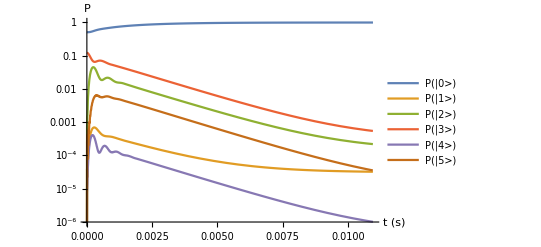

```mathematica
LogPlot[{Evaluate[ρ[t]/.ρs][[1,12,12]],Evaluate[ρ[t]/.ρs][[1,10,10]],Evaluate[ρ[t]/.ρs][[1,8,8]],Evaluate[ρ[t]/.ρs][[1,6,6]],Evaluate[ρ[t]/.ρs][[1,4,4]],Evaluate[ρ[t]/.ρs][[1,2,2]]},{t,0,Ttot},PlotRange->{10^-6,1},PlotLegends->{"P(|0>)","P(|1>)","P(|2>)","P(|3>)","P(|4>)","P(|5>)","P(|6>)"},AxesLabel->{"t (s)","P"}]
```

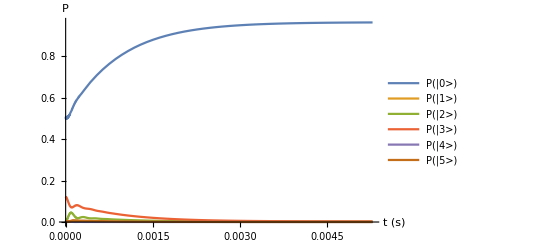

```mathematica
Plot[{Evaluate[ρ[t]/.ρs][[1,12,12]],Evaluate[ρ[t]/.ρs][[1,10,10]],Evaluate[ρ[t]/.ρs][[1,8,8]],Evaluate[ρ[t]/.ρs][[1,6,6]],Evaluate[ρ[t]/.ρs][[1,4,4]],Evaluate[ρ[t]/.ρs][[1,2,2]]},{t,0,Ttot},PlotRange->All,PlotLegends->{"P(|0>)","P(|1>)","P(|2>)","P(|3>)","P(|4>)","P(|5>)","P(|6>)"},AxesLabel->{"t (s)","P"}]
```

```mathematica
ρcool=Table[Abs[Evaluate[ρ[Ttot]/.ρs][[1,i,i]]],{i,12,2,-2}]
```

{0.959617,0.000214042,0.00090019,0.00260822,0.0000119899,0.0000219622}

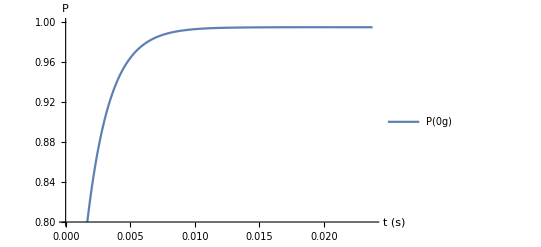

```mathematica
Plot[{Abs[Evaluate[ρ[t]/.ρs][[1,12,12]]]},{t,0,Ttot},PlotRange->{0.8,1},PlotLegends->{"P(0g)"},AxesLabel->{"t (s)","P"}]
```

check to make sure we’re not losing population

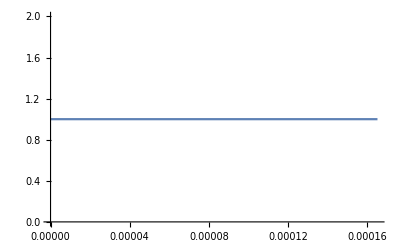

```mathematica
Plot[Sum[Evaluate[ρ[t]/.ρs][[1,i,i]],{i,1,12}],{t,0,Ttot/20},PlotRange->All]
```

## loop over a few raman rabi and pumping rates

```mathematica
numGrid=7;
Pgs=Table[0,{i,1,numGrid},{j,1,numGrid}];
coolingTimes=Table[0,{i,1,numGrid},{j,1,numGrid}];
Ωcs=2π Subdivide[1.*10^3,2*10^4,numGrid-1];
ΩOPs=2π Subdivide[1*10^4,4*10^4,numGrid-1];
For[ii=1,ii≤numGrid,ii++,
For[jj=1, jj≤numGrid, jj++,
Ωc=Ωcs[[ii]];
ΩOP=ΩOPs[[jj]];
Γ3p1=2π*180.*10^3;
Hn=H/.{δ->-ωt,δop->0,ω->ωt,Δls->Δls0,Ω->Ωc,Ωop->ΩOP,ηop->ηOP,η->η0};
OLinn=OLin/.{Γ->Γ3p1,ηop->ηOP};
Ttot=(30π)/(η0 Min[{ΩOP/3,Ωc}]);
ts=Subdivide[0,Ttot,200];
Pns=Table[Pn[n,T0],{n,0,n0}];
Pns[[n0+1]]=1-Sum[Pns[[n+1]],{n,0,n0-1}];
ρs=NDSolve[{I ρ'[t]==Hn.ρ[t]-ρ[t].Hn+I (OLinn.ρ[t].(OLinn†)-1/2 OLinn†.OLinn.ρ[t]-1/2 ρ[t].OLinn†.OLinn),ρ[0]==DiagonalMatrix[Flatten[Table[{0,0,Pns[[n0+1-n]]},{n,0,n0}]]]},ρ,{t,0,Ttot},AccuracyGoal->4, MaxSteps->1000000];
Pgs[[ii,jj]]=Evaluate[ρ[Ttot]/.ρs][[1,3*(n0+1),3*(n0+1)]];
For[i=1,i≤Length[ts],i++,
If[Abs[Evaluate[ρ[ts[[i]]]/.ρs][[1,12,12]]] >0.98 Abs[Evaluate[ρ[Ttot]/.ρs][[1,12,12]]], Break[]]
];
coolingTimes[[ii,jj]]=ts[[i]]; 
Print[{ii,jj}]
]
]
```

{1,1}

{1,2}

{1,3}

{1,4}

{1,5}

{1,6}

{1,7}

{2,1}

{2,2}

{2,3}

{2,4}

{2,5}

{2,6}

{2,7}

{3,1}

{3,2}

{3,3}

{3,4}

{3,5}

{3,6}

{3,7}

{4,1}

{4,2}

{4,3}

{4,4}

{4,5}

{4,6}

{4,7}

{5,1}

{5,2}

{5,3}

{5,4}

{5,5}

{5,6}

{5,7}

{6,1}

{6,2}

{6,3}

{6,4}

{6,5}

{6,6}

{6,7}

{7,1}

{7,2}

{7,3}

{7,4}

{7,5}

{7,6}

{7,7}

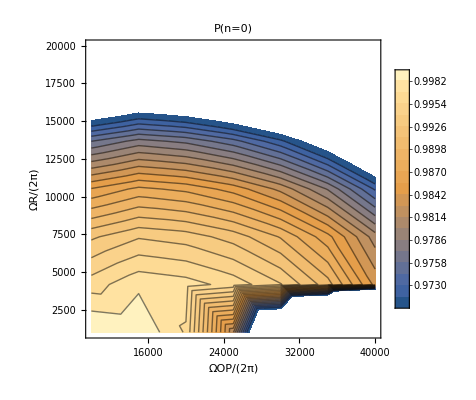

```mathematica
Pgsplot=ArrayFlatten[Table[{ΩOPs[[j]]/(2π),Ωcs[[i]]/(2π),Abs[Pgs[[i,j]]]},{i,1,Length[Pgs]},{j,1,Length[Pgs[[1]]]}],1];
ListContourPlot[Pgsplot,PlotLegends->Automatic,FrameLabel->{"ΩOP/(2π)", "ΩR/(2π)"},Contours->20,PlotRange->{All,All,{0.97,1}},PlotLabel->"P(n=0)"]
```

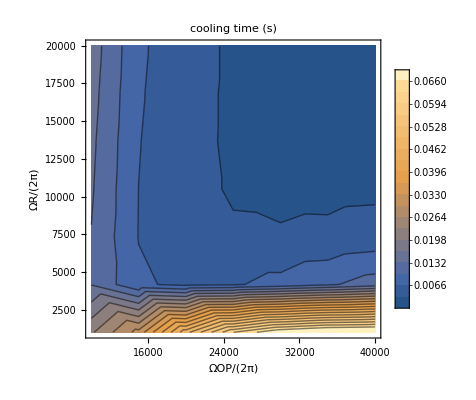

```mathematica
coolingTimesplot=ArrayFlatten[Table[{ΩOPs[[j]]/(2π),Ωcs[[i]]/(2π),Abs[coolingTimes[[i,j]]]},{i,1,Length[coolingTimes]},{j,1,Length[coolingTimes[[1]]]}],1];
ListContourPlot[coolingTimesplot,PlotLegends->Automatic,FrameLabel->{"ΩOP/(2π)", "ΩR/(2π)"},Contours->20,PlotRange->{All,All,All},PlotLabel->"cooling time (s)"]
```

```mathematica
Ttots=Table[0,{i,1,numGrid},{j,1,numGrid}];
coolingTimeRatios=Table[0,{i,1,numGrid},{j,1,numGrid}];
For[ii=1,ii≤numGrid,ii++,
For[jj=1, jj≤numGrid, jj++,
Ωc=Ωcs[[ii]];
ΩOP=ΩOPs[[jj]];
Ttot=(30π)/(η0 Min[{ΩOP/3,Ωc}]);
Ttots[[ii,jj]]=Ttot;
coolingTimeRatios[[ii,jj]]=Abs[coolingTimes[[ii,jj]]]/Ttot;
]
]
```

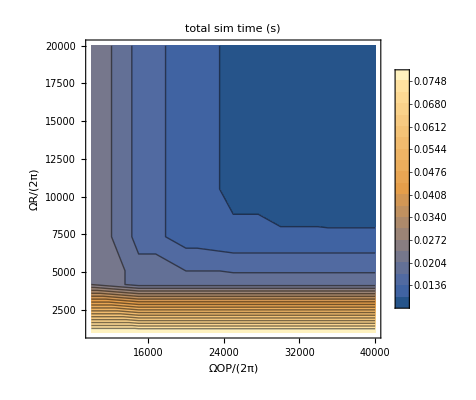

```mathematica
totalTimesplot=ArrayFlatten[Table[{ΩOPs[[j]]/(2π),Ωcs[[i]]/(2π),Abs[Ttots[[i,j]]]},{i,1,Length[Ttots]},{j,1,Length[Ttots[[1]]]}],1];
ListContourPlot[totalTimesplot,PlotLegends->Automatic,FrameLabel->{"ΩOP/(2π)", "ΩR/(2π)"},Contours->20,PlotRange->{All,All,All},PlotLabel->"total sim time (s)"]
```

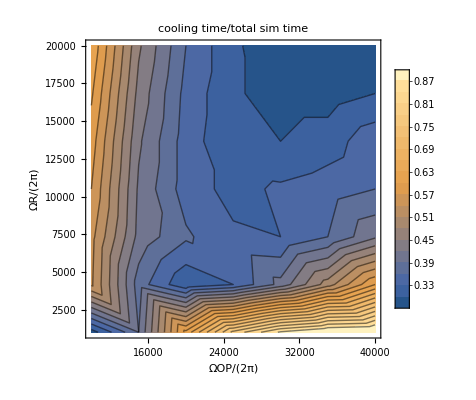

```mathematica
coolingTimeRatiosplot=ArrayFlatten[Table[{ΩOPs[[j]]/(2π),Ωcs[[i]]/(2π),Abs[coolingTimeRatios[[i,j]]]},{i,1,Length[coolingTimeRatios]},{j,1,Length[coolingTimeRatios[[1]]]}],1];
ListContourPlot[coolingTimeRatiosplot,PlotLegends->Automatic,FrameLabel->{"ΩOP/(2π)", "ΩR/(2π)"},Contours->20,PlotRange->{All,All,All},PlotLabel->"cooling time/total sim time"]
```

## gyromagnetic ratios

```mathematica
gj=3/2+(s(s+1)-l(l+1))/(2j(j+1));
gf=gj (f(f+1)-i(i+1)+j(j+1))/(2f(f+1));
```

```mathematica
gf/.{s->1,l->1,j->1,f->3/2,i->1/2}
```

1

```mathematica
gj/.{s->1,l->1,j->1}
```

3/2

```mathematica
dE=gf B μB;
```

```mathematica
μB=9.274*10^-24;
h=6.636*10.^-34;
```

```mathematica
dE/.{s->1,l->1,j->1,f->3/2,i->1/2,B->0.002}
```

1.8548×10^-26

```mathematica
df=dE/h;
```

```mathematica
df/.{s->1,l->1,j->1,f->3/2,i->1/2,B->0.002}
```

2.79506×10^7